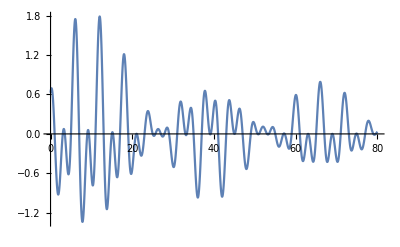

```mathematica
Plot[NIntegrate[(2*n+2)/2 * 2 * π * r*ZernikeR[n, 0, r], {r, a, b}/.a->.4/.b->.6], {n, 0, 80}]
```

```mathematica
integral = ((Gamma[1+n] z^(1+n))/((1+n) Gamma[(1/2) (2-m+n)] Gamma[(1/2) (2+m+n)])) HypergeometricPFQ[{-((n+1)/2),-((m+n)/2),(m-n)/2},{(1-n)/2,-n},1/z^2]
```

(z^(1+n) Gamma[1+n] HypergeometricPFQ[{-1/2-n/2,-m/2-n/2,m/2-n/2},{1/2-n/2,-n},1/z^2])/((1+n) Gamma[1/2 (2-m+n)] Gamma[1/2 (2+m+n)])

-0.456

```mathematica
Integrate[ r*ZernikeR[4, 0, r], r]
```

r^2/2-(3 r^4)/2+r^6

```mathematica
ZernikeR[10, 0, r]
```

-1+30 r^2-210 r^4+560 r^6-630 r^8+252 r^10

SetDelayed::write: Tag Integrate in (∫r ZernikeR[n,0,r]ⅆr)[n_,p_] is Protected.

$Failed

```mathematica
int[1, 1]
```

(∫r ZernikeR[n,0,r]ⅆr)[1,1]

```mathematica
Plot[(2*n+2)/2 * 2 * π * /.r->.4 - Integrate[r*ZernikeR[n, 0, r], r]/.r->.6, {n, 0, 2}]
```

```mathematica
int[n_]:=
Module[{deg=n},m=n;
res = Integrate[r*ZernikeR[n, 0, r], r];
res/.r->.4]
int2[n_]:=
Module[{deg=n},m=n;
res = Integrate[r*ZernikeR[n, 0, r], r];
res/.r->.6]
maxn = 100
r1 = Array[int, maxn]
r2 = Array[int2, maxn]
```

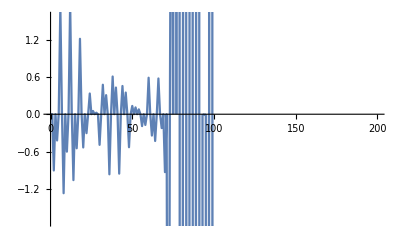

```mathematica
DiscretePlot[(2*n+2)/2 * 2 * π  * (r2[[n]] - r1[[n]]), {n, 0, 200}]
```

```mathematica
int[2,.4]
```

-0.0672

```mathematica
r2-r1
```

{0,-0.048,0,-0.01344,0,0.039552,0,-0.0224717,0,-0.00871477,0,0.0218684,0,-0.0112464,0,-0.00513086,0,0.0101626,0,-0.00405154,0,-0.00210983,0,0.00212194,0,0.000305322,0,0.000135871,0,-0.00252973,0,0.00228772,0,0.00139566,0,-0.00415768,0,0.00247608,0,0.00166597,0,-0.00353721,0,0.00160657,0,0.00118024,0,-0.00172446,0,0.000415609,0,0.000331083,0,0.000227637,0,-0.0005344,0,-0.000466008,0,0.00153184,0,-0.000867172,0,-0.00105369,0,0.00136575,0,-0.000513646,0,-0.00208801,0,-0.0227895,0,0.0149026,0,0.187847,0,0.250214,0,-1.5006,0,4.00059,0,-12.0002,0,63.9997,0,-63.9994,0,639.999,0,-1536.,0,-0.0000190735,0,-4096.,0,8192.,0,-163840.}

-1+2 r^2

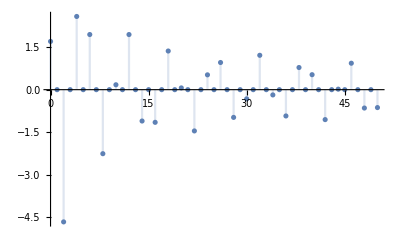

```mathematica
DiscretePlot[ 2 * π  * (2*n+2 )*(Integrate[r*ZernikeR[n, 0, r], r]/.r->6/10 - Integrate[r*ZernikeR[n, 0, r], r]/.r->4/10), {n, 0, 50}, PlotRange->All]
```

```mathematica
Table[(2*n+2 )*(Integrate[r*ZernikeR[n, 0, r], {r, 2/10, 8/10 }])//N, {n, 0, 40}]
```

{0.6,0.,-0.576,0.,-0.4992,0.,0.462336,0.,0.12331,0.,0.211505,0.,-0.485376,0.,-0.0154199,0.,0.113567,0.,0.230244,0.,0.0169068,0.,-0.334181,0.,0.0458214,0.,0.0286091,0.,0.290633,0.,-0.151501,0.,-0.147771,0.,-0.0424233,0.,0.108316,0.,0.212767,0.,-0.182669}

```mathematica
Integrate[r*ZernikeR[0, 0, r], r]/.r->.6 - Integrate[r*ZernikeR[0, 0, r], r]/.r->.4
```

0.1352

```mathematica
NIntegrate[r*ZernikeR[0, 0, r], {r, .4 , .6}, PrecisionGoal->5, AccuracyGoal->5]
```

0.1

```mathematica
foo = Integrate[r*ZernikeR[100, 0, r], r]
Plot[foo, Range[0, 1, 1/100]]
```

r^2/2-(1275 r^4)/2+270725 r^6-57393700 r^8+7283260530 r^10-614221638030 r^12+36853298281800 r^14-1650501287334900 r^16+57171530702961675 r^18-1574122812021544785 r^20+35203110159754547010 r^22-650724157498493141700 r^24+10086224441226643696350 r^26-132672644573058159390450 r^28+1496042011185722483031360 r^30-14586409609060794209555760 r^32+123877228665185421412036050 r^34-922197146729713692734046150 r^36+6050907594331805633026899300 r^38-35158957811275333783482614880 r^40+181654615358255891214660176880 r^42-837498551327023914041615101200 r^44+3455922875831671803397020417600 r^46-12796931808333219503883169807200 r^48+42613782921749620947930955457976 r^50-127841348765248862843792866373928 r^52+346009348509932819662687245171600 r^54-845800629690946892508791043752800 r^56+1868677745893545228030506320803600 r^58-3733059680876990352088528719030640 r^60+6743591681584240636030890589216640 r^62-11012720286458134909647220518680400 r^64+16247933907482740709498456030401575 r^66-21634949427610708217460510970962525 r^68+25961939313132849860952613165155030 r^70-28022410687191012548329804686199080 r^72+27138821161018322963472558592490100 r^74-23510017193542188740760722877420300 r^76+18148083447646601834973189589587600 r^78-12424457129542673563943183642102280 r^80+7500129608687345627014482808342230 r^82-3963483126542093217527978719855650 r^84+1817145087916308518335086589169700 r^86-714564453176391933214220096375400 r^88+237466368782861561643917587583340 r^90-65389289954701009728035277740340 r^92+14517511183282370337399136593600 r^94-2496806001380123976467582002800 r^96+312100750172515497058447750350 r^98-25222836136391048333703124314 r^100+989130828878080326811887228 r^102

Plot::pllim: Range specification Range[0,1,1/100] is not of the form {x, xmin, xmax}.

Plot[foo,Range[0,1,1/100]]

```mathematica
.1^100 * 989130828878080326811887228
```

9.89131×10^-74

```mathematica
Table[foo,  Range[0, 1, 1/100]]
```

Table::nliter: Non-list iterator Range[0,1,1/100] at position 2 does not evaluate to a real numeric value.

```mathematica
ListPlot[foo/@Range[0,1,1/100]]
```

-Graphics-

```mathematica
Map[foo, Range[0, 1, 1/100]]
```

{(r^2/2-(1275 r^4)/2+270725 r^6-57393700 r^8+7283260530 r^10-614221638030 r^12+36853298281800 r^14-1650501287334900 r^16+57171530702961675 r^18-1574122812021544785 r^20+35203110159754547010 r^22-650724157498493141700 r^24+10086224441226643696350 r^26-132672644573058159390450 r^28+36+18148083447646601834973189589587600 r^78-12424457129542673563943183642102280 r^80+7500129608687345627014482808342230 r^82-3963483126542093217527978719855650 r^84+1817145087916308518335086589169700 r^86-714564453176391933214220096375400 r^88+237466368782861561643917587583340 r^90-65389289954701009728035277740340 r^92+14517511183282370337399136593600 r^94-2496806001380123976467582002800 r^96+312100750172515497058447750350 r^98-25222836136391048333703124314 r^100+989130828878080326811887228 r^102)[0],(1)[1/100],98,(75+989130828878080326811887228 r^102)[1]}
 |  |  |  |

```mathematica
summand[r2_, r1_,n_, k_] := (-1)^k * Factorial[n-k]/(Factorial[k] * Factorial[n/2 - k]^2)*(r2^(n-2*k+1) - r1^(n-2*k+1))/(n-2*k+1)
```

```mathematica
n = 20

Q[n_]:=
Module[{total},
 total = 0;
For[k=0, k <= n/2, k++, total+=summand[6/10,4/10, n, k]];
If[Mod[n,2]!=0, 0,total]]
```

20

```mathematica
Q[1]
```

0

```mathematica
(* The following should be correct, i.e. it agrees with my other notebook, and I managed to take it out precision!*)
Table[(2*n+2 )*Q[n]//N, {n, 0, 100}]
```

{0.4,0.,-0.592,0.,-0.22976,0.,1.09453,0.,-0.877215,0.,-0.27192,0.,1.10632,0.,-0.791902,0.,-0.181061,0.,0.72926,0.,-0.476823,0.,-0.0147197,0.,0.167266,0.,-0.0815007,0.,0.154543,0.,-0.350285,0.,0.244945,0.,0.256028,0.,-0.63739,0.,0.401046,0.,0.247566,0.,-0.614905,0.,0.362894,0.,0.133283,0.,-0.332136,0.,0.182562,0.,-0.037335,0.,0.0629506,0.,-0.0422433,0.,-0.190025,0.,0.391215,0.,-0.212534,0.,-0.257808,0.,0.51819,0.,-0.267199,0.,-0.210646,0.,0.40649,0.,-0.20182,0.,-0.0693245,0.,0.124149,0.,-0.0619997,0.,0.103152,0.,-0.192166,0.,0.0828102,0.,0.229327,0.,-0.400853,0.,0.171602,0.,0.252055,0.,-0.417161,0.,0.175931,0.,0.160578}

```mathematica
%2
```

0